## Dynamical System Benchmarks

n: dimension
b: branch
m: number of parameters in template

### Simple (n=2, b=1, m=2)

```mathematica
f={0.9*(x1-0.01x2),0.9*(x2+0.01 x1)};
loopCond=-1; 
preCond=x1^2+x2^2-1;
postCond=1/4 - x1^2-(x2-2)^2;
inv=x1^2+a1*x2^2+a2;
invf = inv/.{x1-> f[[1]],x2-> f[[2]]};
arange = -1≤ a1≤ 1&&-1≤ a2≤ 1;
xrange = -4≤ x1≤ 4&&-4≤ x2≤ 4;
verifyPrecondition = preCond≤ 0&&inv>0&&xrange;
verifyBranch=inv≤ 0&&loopCond≤ 0&&invf>0&&xrange;
verifyPostcondition = inv≤ 0&&postCond>0&&xrange;
```

```mathematica
(*adeg = 2, sdeg = 4*)
aSol=FindInstance[8.72559884158+1.88915832929*a1-4.78619313635*a2+2.94280994265*a1^2-4.22839022103*a1*a2+12.0783087932*a2^2-0.0665173120021*a1^3-3.90431920608*a1^2*a2+6.80492010214*a1*a2^2+1.95390002155*a2^3≤ 0&&arange&& -1≤ a3≤ 1,{a1,a2,a3}];
aSol = aSol[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
aSol= {a1-> 6.75,a2-> -10};
FindInstance[verifyPrecondition/.aSol,{x1,x2}]
FindInstance[verifyBranch/.aSol,{x1,x2}]
FindInstance[verifyPostcondition/.aSol,{x1,x2}]
```

{}

{}

{}

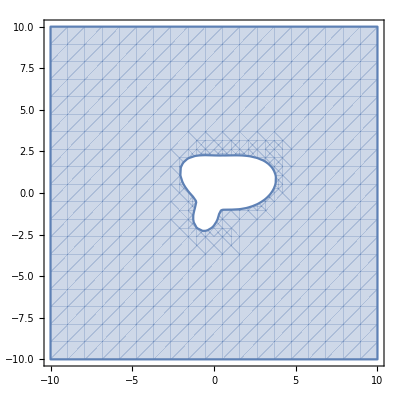

```mathematica
RegionPlot[2.45157643671+3.00825959587*a1+6.72375029844*a2+4.55380260855*a1^2+2.70171260633*a1*a2+4.90964997743*a2^2+1.23996182652*a1^3+2.14138158852*a1^2*a2-2.01964195172*a1*a2^2-1.1365204506*a2^3-0.81495468789*a1^4+0.0432388486489*a1^3*a2-1.71866892718*a1^2*a2^2+0.010106683199*a1*a2^3-1.13620699606*a2^4≤ 0,{a1,-10,10},{a2,-10,10}]
```

```mathematica
RegionPlot[1.86740515472+2.93155644265*a1+6.62405287212*a2+7.06014463909*a1^2+2.84739875178*a1*a2+7.33200946014*a2^2+2.40547137554*a1^3+4.95459135358*a1^2*a2-4.14542678345*a1*a2^2-2.00962637083*a2^3-5.67926702413*a1^4+0.552576087103*a1^3*a2-6.17564549556*a1^2*a2^2-0.262776305105*a1*a2^3-6.15199540355*a2^4-0.95916398156*a1^5-3.55422185137*a1^4*a2-0.463885918625*a1^3*a2^2+0.671872561608*a1^2*a2^3+2.59784036104*a1*a2^4+0.715194929728*a2^5+2.65904458599*a1^6-1.63112122584*a1^5*a2+3.3253622041*a1^4*a2^2+1.68131281856*a1^3*a2^3+1.53861241685*a1^2*a2^4-0.756765666555*a1*a2^5+3.1978074999*a2^6≤ 0,{a1,-10,10},{a2,-10,10}]
```

-Graphics-

### Dubin’s Car (n=2, b=1, m=2)

```mathematica
d = 0.01; 
w = 1.0178+1.8721*x1-0.0253*x2;
f={
x1+d*(1-x2*w),
x2+d*x1*w};
guard=-1; (*always true*)
preCond=x1^2+(x2-1)^2-1;
postCond=x1^2+(x2-1)^2-4;

inv=x1^2+a1*x2^2-2*a1*x2+a2;
invf = inv/.{x1-> f[[1]],x2-> f[[2]]};
rangeCond = 0< x1< 10&&0<x2< 10;
verifyPrecondition = preCond<0&&rangeCond&&inv>0;
verifyBranch=inv≤ 0&&rangeCond&&guard≤ 0&&invf>0;
verifyPostcondition = inv≤  0&&rangeCond&&guard>0&&postCond>0;
```

```mathematica
FindInstance[4.67912100254+12.8493504528*a1+13.3582763853*a2+8.66159682168*a1^2+12.9726438683*a1*a2+8.63496821275*a2^2≤ 0&&-1≤ a1≤ 1&&-1≤ a2≤ 1,{a1,a2}]
```

{{a1→0.0788958,a2→-1.}}

```mathematica
Minimize[1.06150476185-1.7012347538*a1+1.72941573053*a2+0.503858081081*a1^2-0.746850912685*a1*a2+0.42424870767*a2^2+0.331848693276*a1^3-0.225734035276*a1^2*a2+0.67308039922*a1*a2^2-0.248000622483*a2^3+0.102740974106*a1^4+0.26818703733*a1^3*a2+0.180509009601*a1^2*a2^2-0.264368216*a1*a2^3+0.0352214359029*a2^4,{a1,a2}]
```

{-0.0458342,{a1→0.60368,a2→-0.511356}}

```mathematica
aSol = {a1->0.6036802257350706/20+1,a2->-0.5113562373235363*2};
FindInstance[verifyPrecondition/.aSol,{x1,x2}]
FindInstance[verifyBranch/.aSol,{x1,x2}]
FindInstance[verifyPostcondition/.aSol,{x1,x2}]
```

{}

{{x1→0.0859375,x2→2.40909}}

{}

```mathematica
invf/.{x1->0.123046875,x2->2.736842105263158,a1->0.49620764603100986/20+1,a2->-1.0409585245768487*2}
```

0.0000597188

```mathematica
-0.000059541212483749106
inv/.{x1->0.060546875,x2->2.4705882352941178,a1->1.008205091112937104,a2->-0.5879473530817293*2}
```

### Overview example (dim=2, branch=1)

```mathematica
f={x1^2+x2-1,x1*x2+x2+1};
guard=x1^2+x2^2-3;
preCond=x1^2+x2^2-1;
postCond=x1^2-2*x2^2-4;
inv=x1^2+a1*x2^2+a2;
arange = {-5,5,-5,5};
invf = inv/.{x1-> f[[1]],x2-> f[[2]]};
verifyPrecondition = preCond<0&&inv>0;
verifyBranch=inv<0&&guard<0&&invf>0;
verifyPostcondition = inv<0&&guard>0&&postCond>0;
```

```mathematica
(*adeg = 2, sdeg = 8*)
FindInstance[19.333192456+23.2831323029*a1-14.4718777127*a2-4.5801377778*a3+19.0633244755*a1^2-20.3717407531*a1*a2+19.0717543502*a2^2-24.4939406791*a1*a3+13.6658194359*a2*a3+9.35881504469*a3^2+4.82837417255*a1^3-16.1867448362*a1^2*a2-7.34345792346*a1*a2^2+7.54389880552*a2^3-9.35531843264*a1^2*a3+19.3970652059*a1*a2*a3+9.82921215402*a2^2*a3+5.32765185159*a1*a3^2-3.54679109499*a2*a3^2-2.65067258163*a3^3≤ 0&&-1≤ a1≤ 1&&-1≤ a2≤ 1&&-1≤ a3≤ 1,{a1,a2,a3}]
```

{}

```mathematica
aSol = {a1-> -2,a2-> -3.95998};
FindInstance[verifyPrecondition/.aSol,{x1,x2}]
FindInstance[verifyBranch/.aSol,{x1,x2}]
FindInstance[verifyPostcondition/.aSol,{x1,x2}]
```

{}

{{x1→-1.61224,x2→0.610213}}

{}

## Program Benchmarks

### cohendiv (dim=5, branch=1)

```mathematica
f={x,y,d,r,q};
guard=y-r;
preCond=-1;
postCond= x-q*y-y;
inv=-q*y +a1*r + a2*x;
arange = {0.95,1.05,-1.05,0.95};
invf = inv/.{x-> f[[1]],y-> f[[2]],d-> f[[3]],r-> f[[4]],q-> f[[5]]};
xRangeCond = 0≤  x≤  10&&0<r≤  10&&0≤ y≤ 10&&0≤ d≤ 10&&0≤ q≤ 10;
verifyPrecondition = preCond<0&&inv>0&&xRangeCond;
verifyBranch=inv≤ 0&&guard≤ 0&&invf>0&&xRangeCond;
verifyPostcondition = inv≤ 0&&guard>0&&postCond>0&&xRangeCond;
```

```mathematica
aSol={a1-> -0.99,a2-> 1};FindInstance[(verifyBranch/.aSol)&&xRangeCond,{y,x,r,d,q}]
FindInstance[(verifyPostcondition/.aSol)&&xRangeCond,{y,x,r,d,q}]
```

{}

{}

### freire1 (dim=2, branch=1)

```mathematica
f={x-r,r+1};
guard=r-x;
preCond=y-2x;
postCond= y-r^2-r;
inv=y-a1*r^2-a2*r;
arange = {-2,2,-2,2};
invf = inv/.{x-> f[[1]],r-> f[[2]]};
xRangeCond = 0≤  x≤  10&&0<r≤  10&&0≤ y≤ 10;
verifyPrecondition = preCond<0&&inv>0&&xRangeCond;
verifyBranch=inv≤ 0&&guard≤ 0&&invf>0&&xRangeCond;
verifyPostcondition = inv≤ 0&&guard>0&&postCond>0&&xRangeCond;
```

```mathematica
(*adeg = 2, sdeg = 8*)
aSol= FindInstance[0.511153215966+3.24293679102*a1+3.38261011805*a2+1.51227188385*a1^2+3.49723136916*a1*a2+0.939760037221*a2^2-0.155755989095*a1^3-0.490889289324*a1^2*a2-0.31409198575*a1*a2^2+0.273123766981*a2^3+0.207789819268*a1^4-1.35303772908*a1^3*a2-1.29148280475*a1^2*a2^2-0.418178560814*a1*a2^3+0.449606580807*a2^4≤ 0
&&-1≤ a1≤ 1&&-1≤ a2≤ 1,{a1,a2}]
```

{{a1→-1.,a2→0.}}

```mathematica
FindInstance[(verifyPrecondition/.aSol)&&x≥ 0&&r≥ 1,{y,x,r}]
```

```mathematica
aSol={a1->1.1,a2->-1.1};
FindInstance[(verifyBranch/.aSol)&&x≥ 0&&r≥ 0,{y,x,r}]
FindInstance[(verifyPostcondition/.aSol)&&x≥ 0&&r≥ 0,{y,x,r}]
```

{}

{}

```mathematica
Minimize[{0.191975989919-0.0124651137188*a1+1.01213730851*a2+0.0156075345578*a1^2-0.0214900774248*a1*a2+0.864886150722*a2^2,-1≤ a1≤ 1,-1≤ a2≤ 1},{a1,a2}]
```

{-0.104139,{a1→-0.00353239,a2→-0.585171}}